# 1mW

```mathematica
SetDirectory["D:\\Qsync\\QOLab\\Data\\On Resonance Project\\Lab Book 2 (18 Mar 29 -)\\20-09-09\\1mW"];
data1mW=Import[#]&/@FileNames["*csv"];
```

```mathematica
(*Get rid of the words*)
l1=Length[data1mW];
data1=Table[Take[data1mW[[l]],{17,-2}],{l,1,l1}];
(*Let's cut the data by scanning data*)
max=Table[Flatten[Position[data1[[l,All,6]],data1[[l,All,6]]//Max],1]//Min,{l,1,l1}];
min=Table[Flatten[Position[data1[[l,All,6]],data1[[l,All,6]]//Min],1]//Max,{l,1,l1}];
data2=Table[Take[data1[[l]][[All,{2,4}]],{min[[l]],max[[l]]}],{l,1,l1}];
```

```mathematica
(*Align them*)
Dxaias[list_]:=Module[{mean,points,F8721,F8712,ans},
Do[points=Select[FindPeaks[list[[All,2]],l,γ,InterpolationOrder->1],#[[2]]≤(mean)&];
If[500<points[[1,1]]<1300&&points[[-1,1]]>3600&&15>Length[points]≥ 8,Break[]];,{l,1,10,1},{γ,{0.00001,0.0001,0.001}},{mean,{0.8,0.825,0.85,0.9}}];
F8721=-(2.563+0.510);
F8712=+(4.271+0.306);
ans=NSolve[{points[[1,1]]m+a==F8712,points[[-1,1]]m+a==F8721},{m,a}][[1]];
Transpose[{Table[m i+a,{i,1,Length[list]}]/.ans,list[[All,1]]}]
]
```

```mathematica
(*Subtract the scatter pump with alignment*)
scatter=data2[[-1]];
td0=TemporalData[#2,{#},ResamplingMethod->{"Interpolation",InterpolationOrder->1}]&@@Transpose@Dxaias[scatter];
data3=Table[Quiet@{#,#2-td0["PathFunction"]@#}&@@@Dxaias[data2[[l]]],{l,1,l1-1}];
```

```mathematica
(*Normalize the data*)
data4=Table[Select[data3[[l]],-3.5<#[[1]]<6&],{l,1,l1-1}];
```

```mathematica
normal[list_]:=Module[{yaxis},
yaxis=Fit[Flatten[{Take[list,{1,1200}],Take[list,{-250,-1}]},1],{1,x},x]/.x->list[[All,1]];
Transpose[{-list[[All,1]],list[[All,2]]/yaxis}]]
```

```mathematica
data5=Table[normal[data4[[l]]],{l,1,l1-1}];
```

```mathematica
AOM1=3.035-2{1.500,1.501,1.502,1.503,1.505,1.506,1.507,1.508,1.509,1.510,1.511,1.512,1.513,1.514,1.5142,1.5144,1.5146,1.5148,1.515,1.5152,1.5154,1.5156,1.5158,1.516,1.5161,1.5162,1.5163,1.5164,1.5165,1.5166,1.5167,1.5168,1.5169,1.517,1.5171,1.5171,1.5172,1.5173,1.5174,1.5175,1.5176,1.5177,1.5178,1.5179,1.518,1.5181,1.5182,1.5183,1.5184,1.5185,1.5186,1.5187,1.5188,1.5189,1.519,1.5192,1.5194,1.5196,1.5198,1.520,1.521,1.522,1.523,1.524,1.525,1.526,1.527,1.528,1.529,1.530,1.531,1.532,1.533,1.534,1.535,1.536,1.537};
```

```mathematica
data=Flatten[Table[
Transpose[Flatten[{{Table[AOM1[[l]],{i,1,Length[data5[[l]]]}] },Transpose[data5[[l]]-Table[{1.26488+0.210923,0},{k,1,Length[data5[[l]]]}]]},1]]
,{l,1,l1-1}],1];
```

Interpolation::udeg: Interpolation on unstructured grids is currently only supported for InterpolationOrder->1 or InterpolationOrder->All. Order will be reduced to 1.

InterpolatingFunction[{{-0.039, 0.035}, {-7.47574, 2.02417}}, <>]

InterpolatingFunction::dmval: Input value {-0.0399943,-1.99971} lies outside the range of data in the interpolating function. Extrapolation will be used.

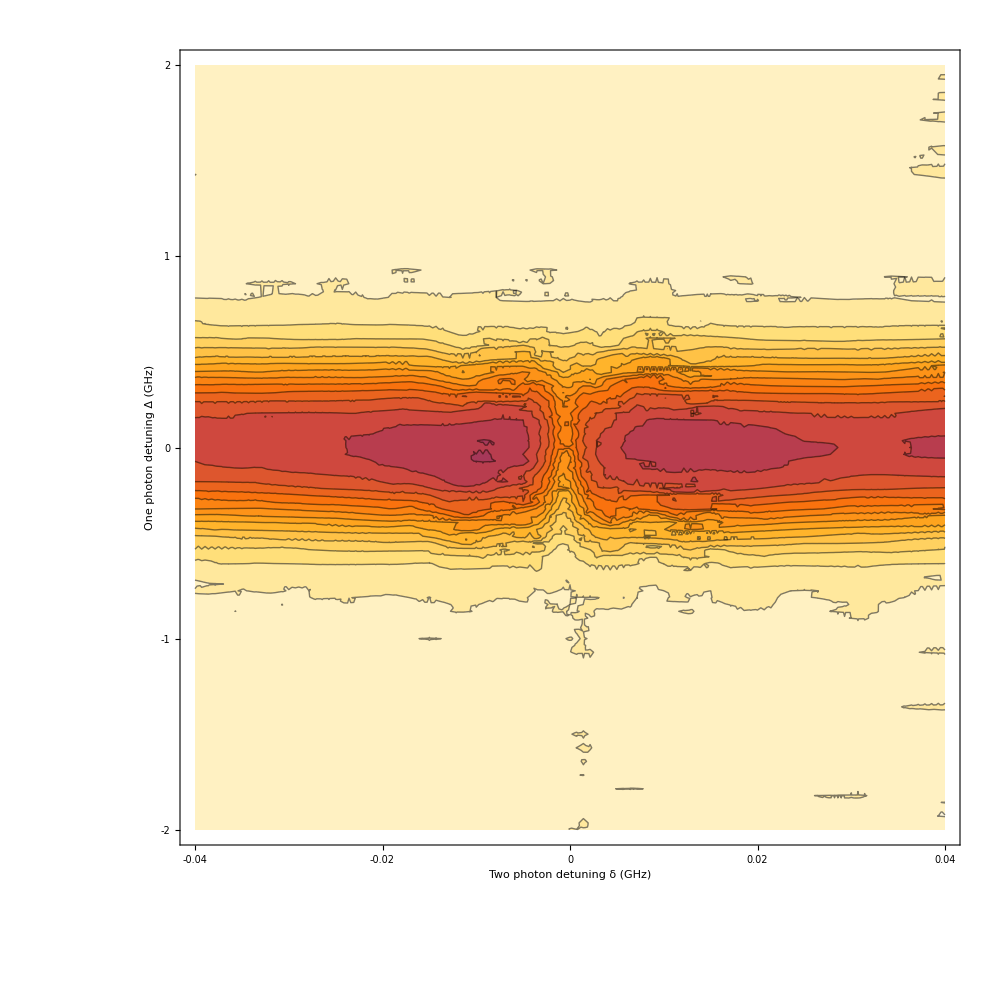

```mathematica
hhh1i=Interpolation[RandomSample[data,100000]]

datra88=ContourPlot[hhh1i[x,y],{x,-0.04,0.04},{y,-2,2},PlotRange->{0,1.1},WorkingPrecision->20,PerformanceGoal->"Quality",ColorFunction->(ColorData["SunsetColors"][Rescale[#,{0,1.1}]]&),ColorFunctionScaling->False,FrameTicks->{{{-2,-1,0,1,2},None},{{-0.04,-0.02,0,0.02,0.04},None}},FrameTicksStyle->Directive[40],Contours->20,ImageSize->1000,FrameLabel->{Style["Two photon detuning δ (GHz)",50,Black],Style["One photon detuning Δ (GHz)",50,Black]}]
```

# 35mW

```mathematica
SetDirectory["D:\\Qsync\\QOLab\\Data\\On Resonance Project\\Lab Book 2 (18 Mar 29 -)\\20-09-09\\35mW"];
data35mW=Import[#]&/@FileNames["*csv"];
```

```mathematica
(*Get rid of the words*)
l1=Length[data35mW];
data1=Table[Take[data35mW[[l]],{17,-2}],{l,1,l1}];
(*Let's cut the data by scanning data*)
max=Table[Flatten[Position[data1[[l,All,6]],data1[[l,All,6]]//Max],1]//Min,{l,1,l1}];
min=Table[Flatten[Position[data1[[l,All,6]],data1[[l,All,6]]//Min],1]//Max,{l,1,l1}];
data2=Table[Take[data1[[l]][[All,{2,4}]],{min[[l]],max[[l]]}],{l,1,l1}];
```

```mathematica
(*Align them*)
Dxaias[list_]:=Module[{mean,points,F8721,F8712,ans},
Do[points=Select[FindPeaks[list[[All,2]],l,γ,InterpolationOrder->1],#[[2]]≤(mean)&];
If[500<points[[1,1]]<1300&&points[[-1,1]]>3600&&15>Length[points]≥ 8,Break[]];,{l,1,10,1},{γ,{0.00001,0.0001,0.001}},{mean,{0.8,0.825,0.85,0.9}}];
F8721=-(2.563+0.510);
F8712=+(4.271+0.306);
ans=NSolve[{points[[1,1]]m+a==F8712,points[[-1,1]]m+a==F8721},{m,a}][[1]];
Transpose[{Table[m i+a,{i,1,Length[list]}]/.ans,list[[All,1]]}]
]
```

```mathematica
(*Subtract the scatter pump with alignment*)
scatter=data2[[-1]];
td0=TemporalData[#2,{#},ResamplingMethod->{"Interpolation",InterpolationOrder->1}]&@@Transpose@Dxaias[scatter];
data3=Table[Quiet@{#,#2-td0["PathFunction"]@#}&@@@Dxaias[data2[[l]]],{l,1,l1-1}];
```

```mathematica
(*Normalize the data*)
data4=Table[Select[data3[[l]],-3.5<#[[1]]<6&],{l,1,l1-1}];
```

```mathematica
normal[list_]:=Module[{yaxis},
yaxis=Fit[Flatten[{Take[list,{1,1200}],Take[list,{-250,-1}]},1],{1,x},x]/.x->list[[All,1]];
Transpose[{-list[[All,1]],list[[All,2]]/yaxis}]]
```

```mathematica
data5M35mW=Table[normal[data4[[l]]],{l,1,l1-1}];
```

```mathematica
AOM35=3.035-2{1.500,1.501,1.502,1.503,1.504,1.505,1.506,1.507,1.508,1.509,1.51,1.511,1.512,1.513,1.514,1.5142,1.5144,1.5146,1.5148,1.515,1.5152,1.5154,1.5156,1.5158,1.516,1.5161,1.5162,1.5163,1.5164,1.5165,1.5166,1.5167,1.5168,1.5169,1.517,1.5171,1.5172,1.5173,1.5174,1.5175,1.5176,1.5177,1.5178,1.5179,1.518,1.5181,1.5182,1.5183,1.5184,1.5185,1.5186,1.5187,1.5188,1.5189,1.519,1.5192,1.5194,1.5196,1.5198,1.520,1.521,1.522,1.523,1.524,1.525,1.526,1.527,1.528,1.529,1.53,1.531,1.532,1.533,1.534,1.535,1.536,1.537,1.538};
```

```mathematica
l1=Length[data35mW];
data35=Flatten[Table[
Transpose[Flatten[{{Table[-AOM35[[l]],{i,1,Length[data5M35mW[[l]]]}] },Transpose[data5M35mW[[l]]-Table[{1.26488+0.210923,0},{k,1,Length[data5M35mW[[l]]]}]
]},1]]
,{l,1,l1-1}],1];
```

Interpolation::udeg: Interpolation on unstructured grids is currently only supported for InterpolationOrder->1 or InterpolationOrder->All. Order will be reduced to 1.

InterpolatingFunction[{{-0.035, 0.039}, {-7.47561, 2.02416}}, <>]

InterpolatingFunction::dmval: Input value {-0.0399943,-1.99971} lies outside the range of data in the interpolating function. Extrapolation will be used.

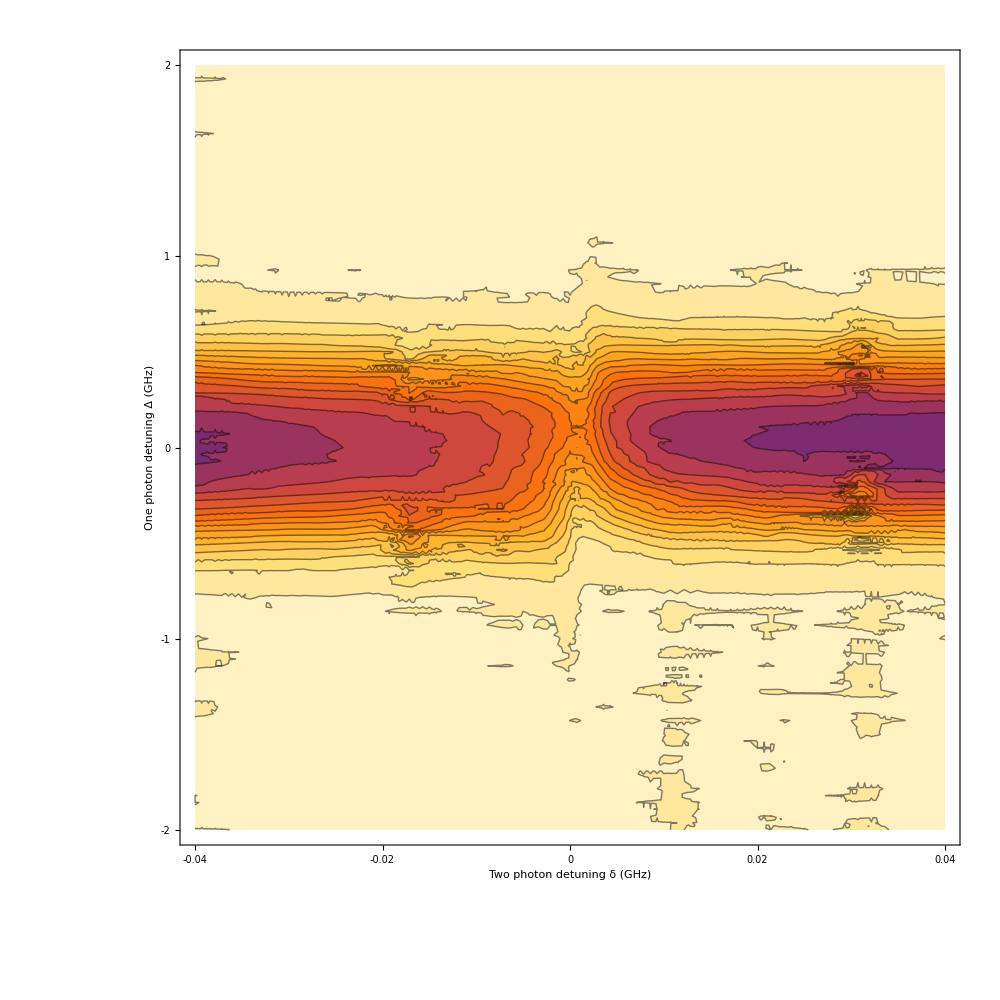

```mathematica
hhh1i=Interpolation[RandomSample[data35,100000]]

datra88=ContourPlot[hhh1i[x,y],{x,-0.04,0.04},{y,-2,2},PlotRange->{0,1.1},WorkingPrecision->20,PerformanceGoal->"Quality",ColorFunction->(ColorData["SunsetColors"][Rescale[#,{0,1.1}]]&),ColorFunctionScaling->False,FrameTicks->{{{-2,-1,0,1,2},None},{{-0.04,-0.02,0,0.02,0.04},None}},FrameTicksStyle->Directive[40],Contours->20,ImageSize->1000,FrameLabel->{Style["Two photon detuning δ (GHz)",50,Black],Style["One photon detuning Δ (GHz)",50,Black]}]
```

# 100mW

```mathematica
SetDirectory["D:\\Qsync\\QOLab\\Data\\On Resonance Project\\Lab Book 2 (18 Mar 29 -)\\20-09-09\\100mW"];
data100mW=Import[#]&/@FileNames["*csv"];
```

```mathematica
(*Get rid of the words*)
l1=Length[data100mW];
data1=Table[Take[data100mW[[l]],{17,-2}],{l,1,l1}];
(*Let's cut the data by scanning data*)
max=Table[Flatten[Position[data1[[l,All,6]],data1[[l,All,6]]//Max],1]//Min,{l,1,l1}];
min=Table[Flatten[Position[data1[[l,All,6]],data1[[l,All,6]]//Min],1]//Max,{l,1,l1}];
data2=Table[Take[data1[[l]][[All,{2,4}]],{min[[l]],max[[l]]}],{l,1,l1}];
```

```mathematica
(*Align them*)
Dxaias[list_]:=Module[{mean,points,F8721,F8712,ans},
Do[points=Select[FindPeaks[list[[All,2]],l,γ,InterpolationOrder->1],#[[2]]≤(mean)&];
If[500<points[[1,1]]<1300&&points[[-1,1]]>3700&&15>Length[points]≥ 8,Break[]];,{l,1,10,1},{γ,{0.00001,0.0001,0.001}},{mean,{0.8,0.825,0.85,0.9,0.95,1}}];
F8721=-(2.563+0.510);
F8712=+(4.271+0.306);
ans=NSolve[{points[[1,1]]m+a==F8712,points[[-1,1]]m+a==F8721},{m,a}][[1]];
Transpose[{Table[m i+a,{i,1,Length[list]}]/.ans,list[[All,1]]}]
]
```

```mathematica
(*Subtract the scatter pump with alignment*)
scatter=data2[[-1]];
td0=TemporalData[#2,{#},ResamplingMethod->{"Interpolation",InterpolationOrder->1}]&@@Transpose@Dxaias[scatter];
data3=Table[Quiet@{#,#2-td0["PathFunction"]@#}&@@@Dxaias[data2[[l]]],{l,1,l1-1}];
```

```mathematica
(*Normalize the data*)
data4=Table[Select[data3[[l]],-4.5<#[[1]]<6&],{l,1,l1-1}];
```

```mathematica
normal[list_]:=Module[{yaxis},
yaxis=Fit[Flatten[{Take[list,{1,1400}],Take[list,{-250,-1}]},1],{1,x},x]/.x->list[[All,1]];
Transpose[{-list[[All,1]],list[[All,2]]/yaxis}]]
```

```mathematica
data5M100mW=Table[normal[data4[[l]]],{l,1,l1-1}];
```

```mathematica
AOM=3.035-2{1.500,1.501,1.502,1.503,1.504,1.505,1.506,1.507,1.5072,1.5074,1.5076,1.5078,1.508,1.5082,1.5084,1.5086,1.5088,1.509,1.5092,1.5094,1.5096,1.5098,1.510,1.5102,1.5104,1.5106,1.5108,1.511,1.5112,1.5114,1.5116,1.5118,1.512,1.5122,1.5124,1.5126,1.5128,1.513,1.5132,1.5134,1.5136,1.5138,1.514,1.5142,1.5144,1.5146,1.5148,1.515,1.5152,1.5154,1.5156,1.5158,1.516,1.5161,1.5162,1.5163,1.5164,1.5165,1.5166,1.5167,1.5168,1.5169,1.517,1.5171,1.5172,1.5173,1.5174,1.5175,1.5176,1.5177,1.5178,1.5179,1.518,1.5181,1.5182,1.5183,1.5184,1.5185,1.5186,1.5187,1.5188,1.5189,1.519,1.5192,1.5194,1.5196,1.5198,1.520,1.5202,1.5204,1.5206,1.5208,1.521,1.5212,1.5214,1.5216,1.5218,1.522,1.5222,1.5224,1.5226,1.5228,1.523,1.5232,1.5234,1.5236,1.5238,1.524,1.5242,1.5244,1.5246,1.5248,1.525,1.5252,1.5254,1.5256,1.5258,1.526,1.5264,1.5266,1.5268,1.527,1.5272,1.5274,1.5276,1.5278,1.528,1.5282,1.5284,1.5286,1.5288,1.529,1.53,1.531,1.532,1.533,1.534,1.535,1.536,1.537,1.538,1.539,1.540,1.541,1.542,1.543,1.544};
```

```mathematica
l1=Length[data5M100mW];
data100=Flatten[Table[
Transpose[Flatten[{{Table[-AOM[[l]],{i,1,Length[data5M100mW[[l]]]}] },Transpose[data5M100mW[[l]]-Table[{1.26488+0.210923,0},{k,1,Length[data5M100mW[[l]]]}]
]},1]]
,{l,1,l1-1}],1];
```

Interpolation::udeg: Interpolation on unstructured grids is currently only supported for InterpolationOrder->1 or InterpolationOrder->All. Order will be reduced to 1.

InterpolatingFunction[{{-0.035, 0.047}, {-7.47542, 3.02416}}, <>]

InterpolatingFunction::dmval: Input value {-0.0399943,-1.99971} lies outside the range of data in the interpolating function. Extrapolation will be used.

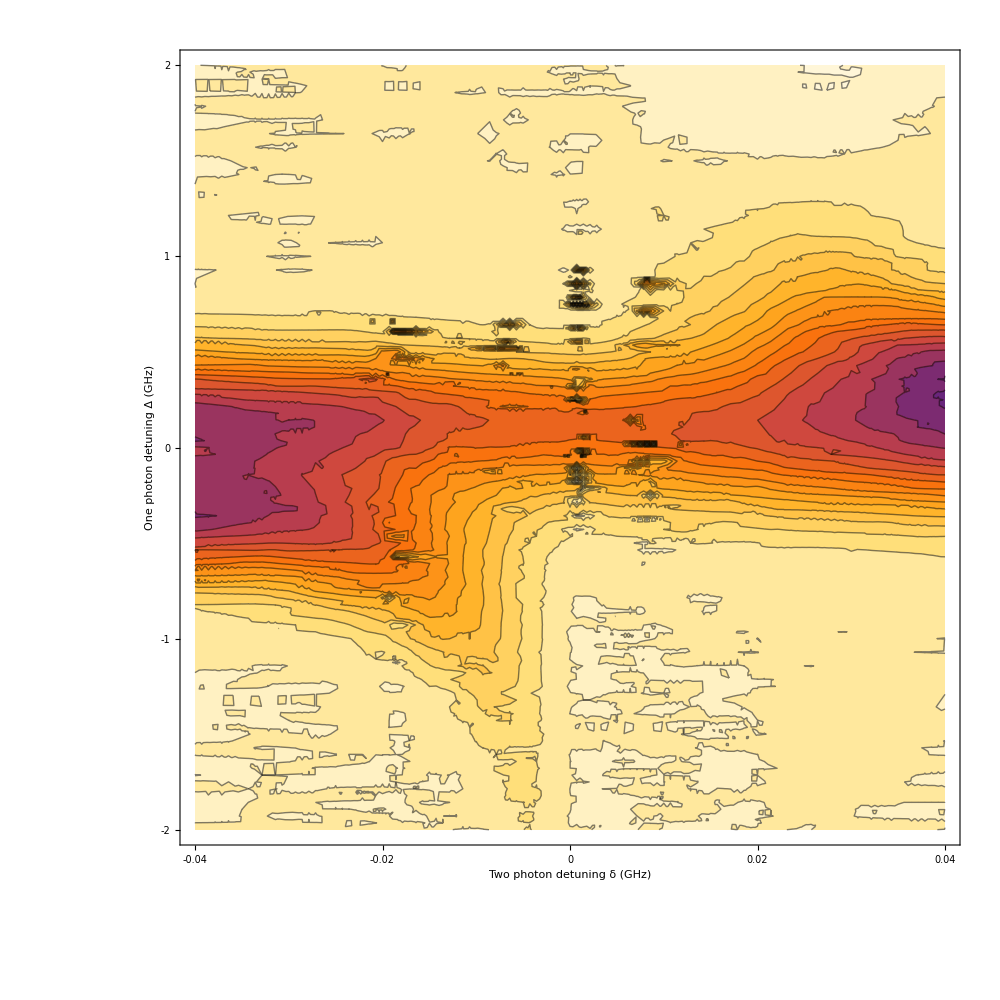

```mathematica
hhh1i=Interpolation[RandomSample[data100,100000]]

datra88=ContourPlot[hhh1i[x,y],{x,-0.04,0.040},{y,-2,2},PlotRange->{0,1.1},WorkingPrecision->20,PerformanceGoal->"Quality",ColorFunction->(ColorData["SunsetColors"][Rescale[#,{0,1.1}]]&),ColorFunctionScaling->False,FrameTicks->{{{-2,-1,0,1,2},None},{{-0.04,-0.02,0,0.02,0.04},None}},FrameTicksStyle->Directive[40],Contours->20,ImageSize->1000,FrameLabel->{Style["Two photon detuning δ (GHz)",50,Black],Style["One photon detuning Δ (GHz)",50,Black]}]
```

## d

{{0.324,0.784},{0.324,0.784},{0.328,0.784},{0.324,0.784},{0.324,0.784},{0.328,0.784},{0.324,0.784},{0.324,0.784},{0.324,0.784},{0.324,0.784},{0.324,0.784},{0.324,0.784},5355,{0.372,0.952},{0.372,0.96},{0.372,0.952},{0.376,0.952},{0.372,0.952},{0.372,0.952},{0.372,0.952},{0.372,0.952},{0.376,0.952},{0.372,0.952},{0.376,0.952}}
 |  |  |  |

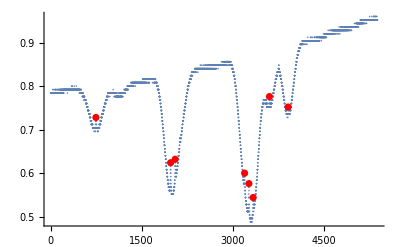

{{6.38091,0.324},{6.37849,0.324},{6.37607,0.328},{6.37366,0.324},{6.37124,0.324},{6.36882,0.328},{6.3664,0.324},{6.36398,0.324},{6.36156,0.324},{6.35914,0.324},{6.35672,0.324},{6.3543,0.324},{6.35188,0.324},{6.34946,0.324},5351,{-6.60098,0.372},{-6.6034,0.372},{-6.60582,0.372},{-6.60824,0.372},{-6.61066,0.372},{-6.61308,0.376},{-6.6155,0.372},{-6.61792,0.372},{-6.62034,0.372},{-6.62275,0.372},{-6.62517,0.376},{-6.62759,0.372},{-6.63001,0.376}}
 |  |  |  |

```mathematica
list=data2[[1]]
Do[points=Select[FindPeaks[list[[All,2]],l,γ,InterpolationOrder->1],#[[2]]≤(mean)&];
If[500<points[[1,1]]<1300&&points[[-1,1]]>3700&&15>Length[points]≥ 8,Break[]];,{l,1,10,1},{γ,{0.00001,0.0001,0.001}},{mean,{0.8,0.825,0.85,0.9,0.95,1}}];
Show[ListPlot[list[[All,2]]],ListPlot[points,PlotStyle->Red]]
F8721=-(2.563+0.510);
F8712=+(4.271+0.306);
ans=NSolve[{points[[1,1]]m+a==F8712,points[[-1,1]]m+a==F8721},{m,a}][[1]];
Transpose[{Table[m i+a,{i,1,Length[list]}]/.ans,list[[All,1]]}]
```

# Compare

## Modeul

```mathematica
χ3a=(4 d32^2 Nat (γ21+ⅈ δ))/(e0 (4 (γ21+ⅈ δ) (-ⅈ γ32+δ+Δ)-ⅈ Ωc^2) ℏ);  
χ3e=(4 d32^2 Nat (γ21-ⅈ δ))/(e0 (4 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ)+ⅈ Ωc^2) ℏ);
```

```mathematica
s3a=χ3a/.Δ->Δ+wc v/c/.δ->δ;
s3a=s3a/.Nat-> Nat/(u Sqrt[Pi])Exp[-v^2/u^2]//ExpandAll//FullSimplify;
s3e=χ3e/.Δ->Δ+wc v/c/.δ->δ;
s3e=s3e/.Nat-> Nat/(u Sqrt[Pi])Exp[-v^2/u^2]//ExpandAll//FullSimplify;
```

```mathematica
χ42=(d42^2 Nat ((4 √5-5 √14) omegac1^2+16 √5 (γ21+ⅈ δ) (γ32+ⅈ (δ+Δ))))/(2 √5 e0 (omegac1^2 (2 w43-7 ⅈ γ32-2 ⅈ γ42+9 δ+9 Δ)+8 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))) ℏ);
χ32=-(d32^2 Nat ((-35+2 √70) omegac1^2+40 (-ⅈ γ21+δ) (w43-ⅈ γ42+δ+Δ)))/(5 e0 (omegac1^2 (2 w43-7 ⅈ γ32-2 ⅈ γ42+9 δ+9 Δ)+8 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))) ℏ);
χ24=(d42^2 Nat (ⅈ (4 √5-5 √14) omegac1^2+16 √5 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ)))/(2 √5 e0 (8 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ) (w43+ⅈ γ42+δ+Δ)+ⅈ omegac1^2 (2 w43+7 ⅈ γ32+2 ⅈ γ42+9 δ+9 Δ)) ℏ);
χ23=(d32^2 Nat ((35 √2-4 √35) omegac1^2-40 ⅈ √2 (γ21-ⅈ δ) (w43+ⅈ γ42+δ+Δ)))/(5 √2 e0 (omegac1^2 (2 w43+7 ⅈ γ32+2 ⅈ γ42+9 δ+9 Δ)+8 (γ21-ⅈ δ) (w43+ⅈ γ42+δ+Δ) (γ32-ⅈ (δ+Δ))) ℏ);
```

```mathematica
s42=χ42/.Δ->Δ+wc v/c/.δ->δ;
s42=s42/.Nat-> Nat/(u Sqrt[Pi])Exp[-v^2/u^2]//ExpandAll//FullSimplify;
s32=χ32/.Δ->Δ+wc v/c/.δ->δ;
s32=s32/.Nat-> Nat/(u Sqrt[Pi])Exp[-v^2/u^2]//ExpandAll//FullSimplify;
s23=χ23/.Δ->Δ+wc v/c/.δ->δ;
s23=s23/.Nat-> Nat/(u Sqrt[Pi])Exp[-v^2/u^2]//ExpandAll//FullSimplify;
s24=χ24/.Δ->Δ+wc v/c/.δ->δ;
s24=s24/.Nat-> Nat/(u Sqrt[Pi])Exp[-v^2/u^2]//ExpandAll//FullSimplify;
```

```mathematica
(*Assuming[u> 0&&u∈Reals&&α1∉Reals&&α2∉Reals,Integrate[((v +Zα)ⅇ^(-v^2/u^2))/((v-α1)(v-α2)),{v,-∞,∞}]]*)
```

```mathematica
Dopp3[χ_]:=Module[{num,den,A,ans,α1,α2,Zα,Int},
num=Numerator[χ];
den=Denominator[χ] ⅇ^(-v^2/u^2);
A=num/CoefficientList[den,v][[2]]//FullSimplify;

α1=CoefficientList[den,v][[1]]/CoefficientList[den,v][[2]]//FullSimplify;
Int=A ⅇ^(-α1^2/u^2) (ⅈ π Erfc[I α1/u])
(*Int=A (π 2 /Sqrt[π] DawsonF[α1/u]-Log[-1/α1] ⅇ^(-α1^2/u^2)-Log[α1] ⅇ^(-α1^2/u^2))//Simplify*)
]
```

```mathematica
Dopp[χ_]:=Module[{num,den,A,ans,α1,α2,Zα,Int},
num=Numerator[χ];
den=Denominator[χ] ⅇ^(-v^2/u^2);
A=CoefficientList[num,v][[2]]/CoefficientList[den,v][[3]];
ans=Solve[den/CoefficientList[den,v][[3]]==0,v];
α1=ans[[1,1,2]]//FullSimplify;
α2=ans[[2,1,2]]//FullSimplify;
Zα= CoefficientList[num,v][[1]]/CoefficientList[num,v][[2]]//FullSimplify;
Int=A(-ⅇ^(-α1^2/u^2) (Zα+α1) (-I π (Erfc[-I α1/u]))+ⅇ^(-α2^2/u^2) (Zα+α2) (-I π (Erfc[-I α2/u])))/(α1-α2)
(*Int=A(- (Zα+α1) (π 2 /Sqrt[π] DawsonF[α1/u]-ⅈ π ⅇ^(-α1^2/u^2))+ (Zα+α2) (π 2 /Sqrt[π] DawsonF[α2/u]-ⅈ π ⅇ^(-α2^2/u^2)))/(α1-α2)*)

]
```

```mathematica
sd32[wc_,γ21_,γ42_,γ32_,δ_,Δ_,omegac1_,c_,ℏ_,e0_,u_,Nat_,w43_,d32_]:=Evaluate[Dopp[s32]];
(*sd23[wc_,γ21_,γ42_,γ32_,δ_,Δ_,omegac1_,c_,ℏ_,e0_,u_,Nat_,w43_,d32_]:=Evaluate[Dopp[s23]];
sd24[wc_,γ21_,γ42_,γ32_,δ_,Δ_,omegac1_,c_,ℏ_,e0_,u_,Nat_,w43_,d42_]:=Evaluate[Dopp[s24]];*)
sd42[wc_,γ21_,γ42_,γ32_,δ_,Δ_,omegac1_,c_,ℏ_,e0_,u_,Nat_,w43_,d42_]:=Evaluate[Dopp[s42]];
sd3a[wc_,γ21_,γ32_,δ_,Δ_,Ωc_,c_,ℏ_,e0_,u_,Nat_,d32_]:=Evaluate[Dopp3[s3a]];
sd3e[wc_,γ21_,γ32_,δ_,Δ_,Ωc_,c_,ℏ_,e0_,u_,Nat_,d32_]:=Evaluate[Dopp3[s3e]];
```

```mathematica
Rbpress[T_]:=
(*
Calculates the vapor pressure of Na depending on the temprerature of the cell.;
Input variable: T:temperature[C];
Output variable: p=Na pressure[torr];
Formulas obtained from "Sodium D Line Data" by Daniel A.Steck;
http://steck.us/alkalidata
*)

Module[{T1,p,k,c,MRb,w0,Nat,dopp},
T1=T+273.15;
(*If[T1<39.31+273.15,p=10^(-94.04826-1961.258/T1-0.03771687*T1+42.57526*Log[10,T1])
,p=10^(15.88253-4529.635/T1+0.00058663*T1-2.99138*Log[10,T1])
];*)
p= If[T1<312.5,10^(9.863-4215/T1),10^(9.318-4040/T1)];(*Unit is in Pa*)
k=1.3806503 10^-23; (*Boltzman's contstant[J/K]*)
c=2.99792458 10^8;(*Speed of light[m/s]*)
MRb=1.409993119 10^-25;(*Rb 85 atomic mass[kg]*)
(*w0=2Pi 377.107385*10^12;(*Transition frequency for 85Rb D1 line*)
dopp=w0/c*Sqrt[2 k*T1/MRb];*)
w0=2Pi 377.107385*10^12;
dopp=2 w0/c*Sqrt[2 Log[2 ]k*T1/MRb]/(2Pi);
Nat=p/(k*T1); (*units in m^-3*)

{Nat,dopp,p,Sqrt[3k*T1/MRb]}
]
```

```mathematica
Lev3DoppTestsc[T_,P_,diam_,gam_,delt_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,Ωc1,Ωc2,Δ2,d31,d41},
d=Range[-0.6,0.4,0.0001]*10^9;
Δ2=2Pi d;(*Raman detuning*)
Δ=2Pi delt;
δ=Δ2-Δ;
Nat=Rbpress[T][[1]];
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(210.923*10^6) +2Pi(150.659*10^6) ;
u=Rbpress[T][[4]]; 

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d32*Sqrt[P/(Pi*(diam/2)^2)]); 


Ωc1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
Ωc2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 

Transpose[{(d-delt)/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]+Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])]}]
]
```

```mathematica
Lev4DoppTestsc[T_,P_,diam_,gam_,delt_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,Δ2,d31,d41},
d=Range[-0.04,0.04,0.0001]*10^9;
Δ2=2Pi d;(*Raman detuning*)
Δ=2Pi delt;
δ=Δ2-Δ;
Nat=Rbpress[T][[1]];
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(210.923*10^6) +2Pi(150.659*10^6) ;
u=Rbpress[T][[4]]; 

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 

Transpose[{(d-delt)/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d42]]+Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]])]
}]

]
```

```mathematica
Lev4DoppTestv[T_,P_,diam_,gam_,delt_,ab_,kk_:0] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,d31,d41},
d=Range[-5,5,0.05]*10^9;
Δ=2Pi d;(*Raman detuning*)
Nat=Rbpress[T][[1]];
δ=2Pi delt;
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi ((210.923*10^6) +(150.659*10^6) );
u=Rbpress[T][[4]]; 

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 

If[ab==0,
{Transpose[{d/10^9,Im[sd24[wc,γ21,γ42,γ32,δ,Δ,omegac2,c,ℏ,e0,u,Nat,w43,d42]]}],
Transpose[{d/10^9,Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac2,c,ℏ,e0,u,Nat,w43,d42]]}],
Transpose[{d/10^9,Im[sd23[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]]}],
Transpose[{d/10^9,Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]]}]
},
Transpose[{If[kk==0,d/( 10^9),(d/10^9+kk)],
Exp[-2Pi*0.0254/(2wcn)(Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d42]]+Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]])]
}]
]
]
```

## pl

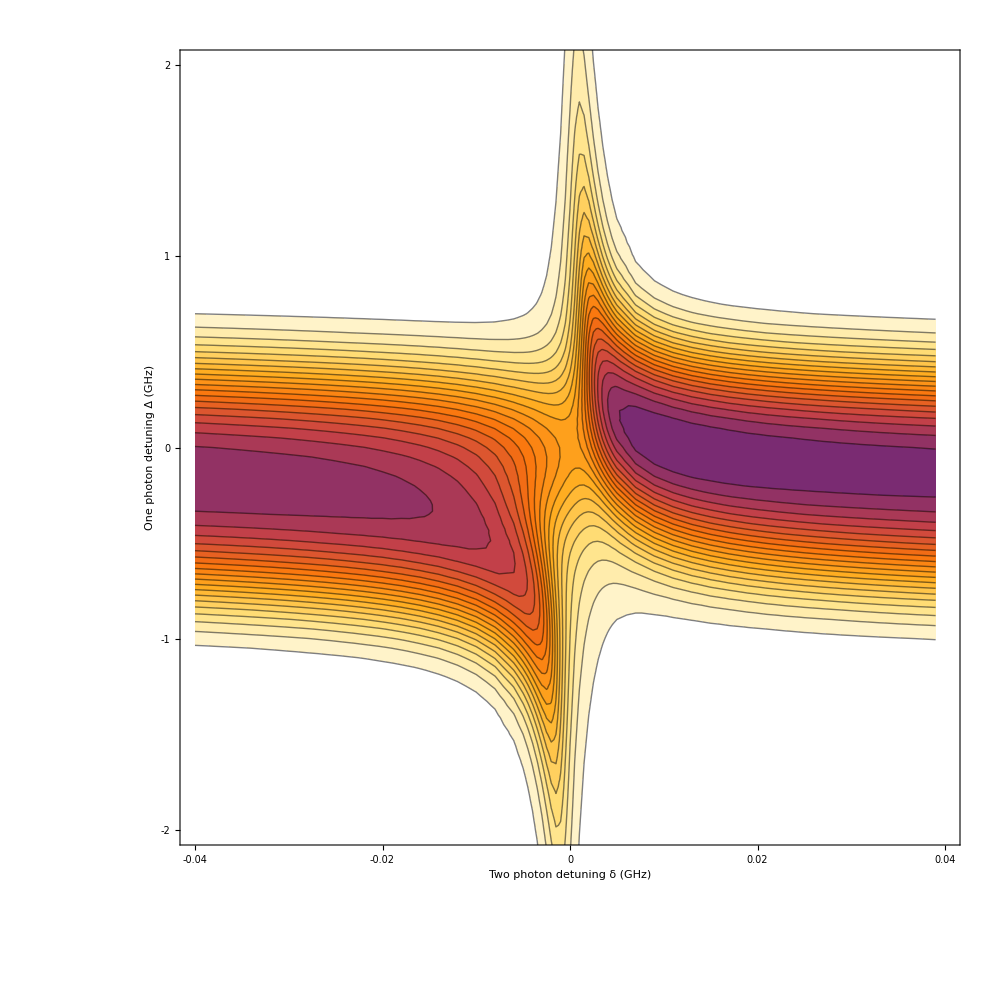

```mathematica
kkkkkk5=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev4DoppTestv[47,35/1000,1.0/1000,1.438*10^6,delt*10^9,1,0]}],{delt,
Flatten[{Range[-0.040,-0.005,0.002],Range[-0.005,0.005,0.0005],Range[0.005,0.04,0.002]}]}]],3];
Kiakkk5=ListContourPlot[kkkkkk5,Contours->25,FrameTicks->{{{-3,-2,-1,0,1,2,3},None},{{-0.04,-0.02,0,0.02,0.04},None}},FrameTicksStyle->Directive[40]
,ImageSize->1000,ColorFunction->(ColorData["SunsetColors"][Rescale[#,{0,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic,PlotRange->{{-0.04,0.04},{-2,2},{0,1}},FrameLabel->{Style["Two photon detuning δ (GHz)",50,Black],Style["One photon detuning Δ (GHz)",50,Black]}]
```

$Aborted

$Aborted

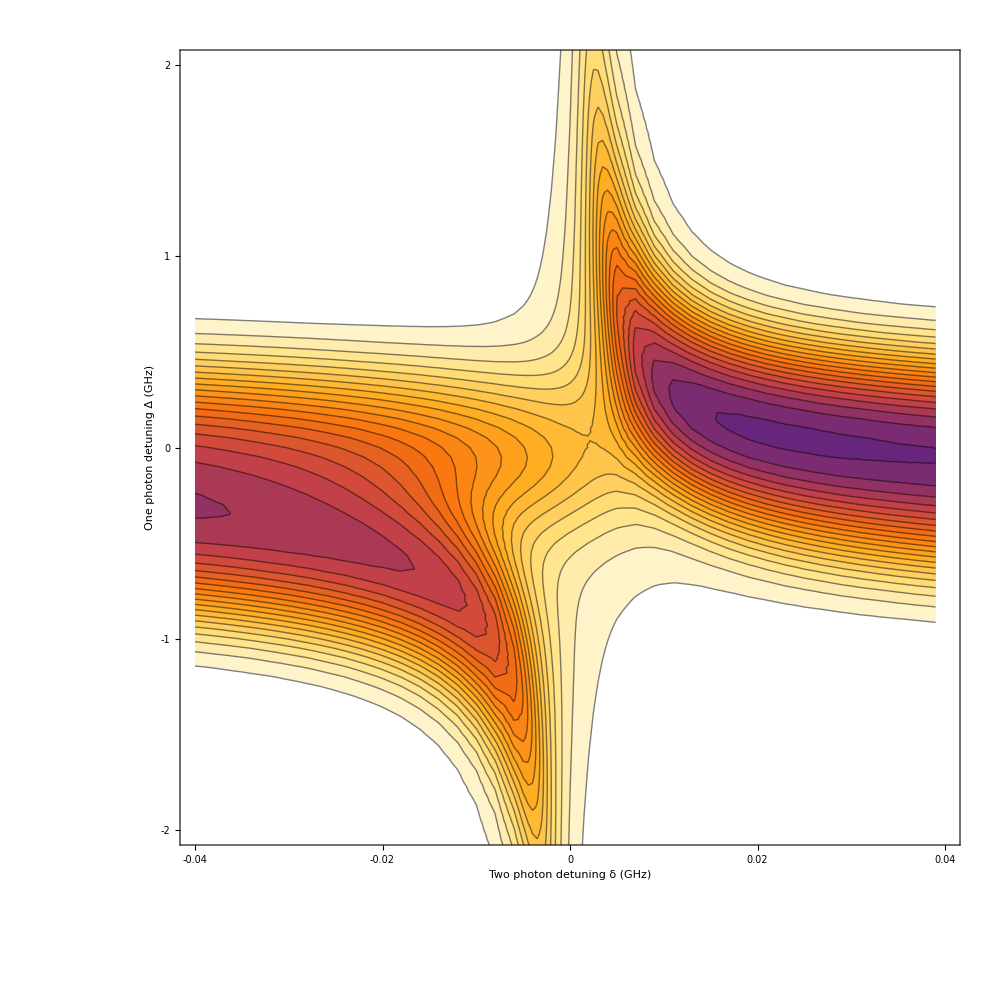

```mathematica
kkkkkk5=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev4DoppTestv[47,100/1000,1.0/1000,2*10^6,delt*10^9,1,0]}],{delt,
Flatten[{Range[-0.040,-0.005,0.002],Range[-0.005,0.005,0.0005],Range[0.005,0.04,0.002]}]}]],3];
Kiakkk5=ListContourPlot[kkkkkk5,Contours->25,FrameTicks->{{{-3,-2,-1,0,1,2,3},None},{{-0.04,-0.02,0,0.02,0.04},None}},FrameTicksStyle->Directive[40]
,ImageSize->1000,ColorFunction->(ColorData["SunsetColors"][Rescale[#,{0,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic,PlotRange->{{-0.04,0.04},{-2,2},{0,1}},FrameLabel->{Style["Two photon detuning δ (GHz)",50,Black],Style["One photon detuning Δ (GHz)",50,Black]}]
```

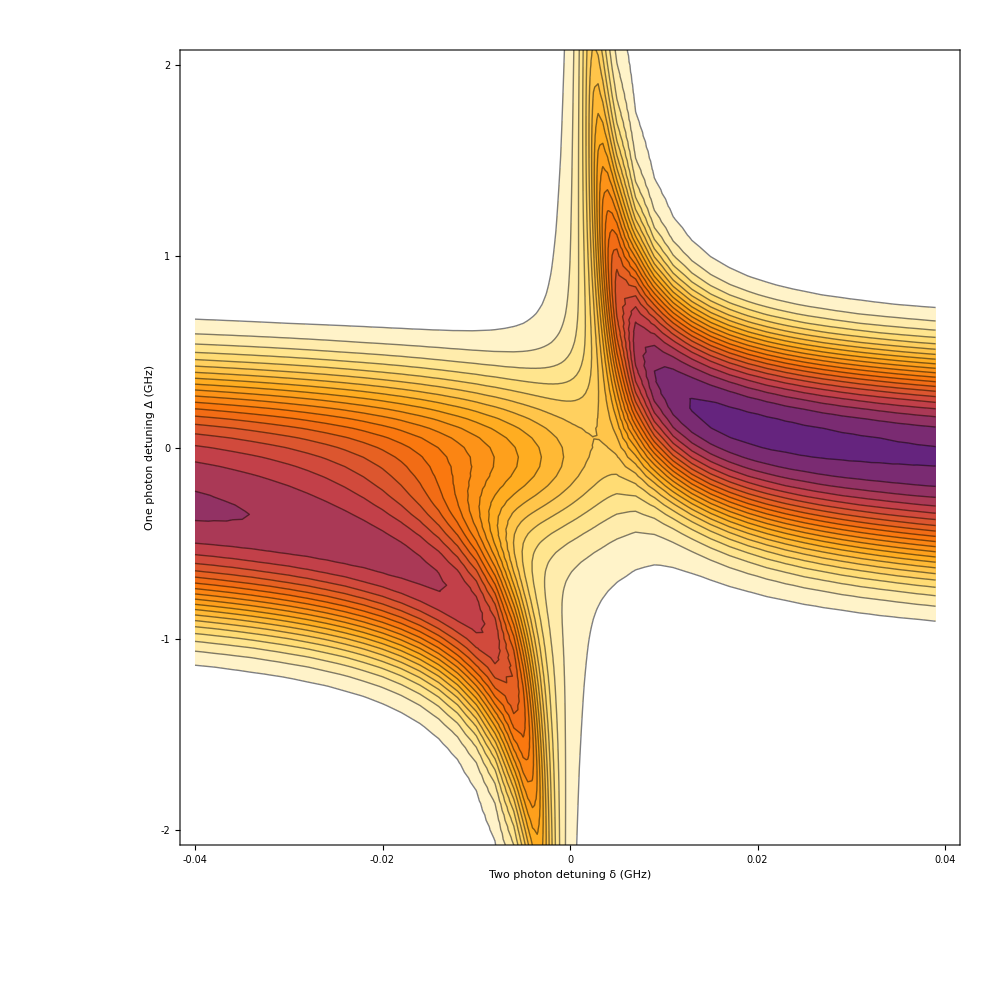

```mathematica
kkkkkk5=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev4DoppTestv[47,100/1000,1.0/1000,1.438*10^6,delt*10^9,1,0]}],{delt,
Flatten[{Range[-0.040,-0.005,0.002],Range[-0.005,0.005,0.0005],Range[0.005,0.04,0.002]}]}]],3];
Kiakkk5=ListContourPlot[kkkkkk5,Contours->25,FrameTicks->{{{-3,-2,-1,0,1,2,3},None},{{-0.04,-0.02,0,0.02,0.04},None}},FrameTicksStyle->Directive[40]
,ImageSize->1000,ColorFunction->(ColorData["SunsetColors"][Rescale[#,{0,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic,PlotRange->{{-0.04,0.04},{-2,2},{0,1}},FrameLabel->{Style["Two photon detuning δ (GHz)",50,Black],Style["One photon detuning Δ (GHz)",50,Black]}]
```

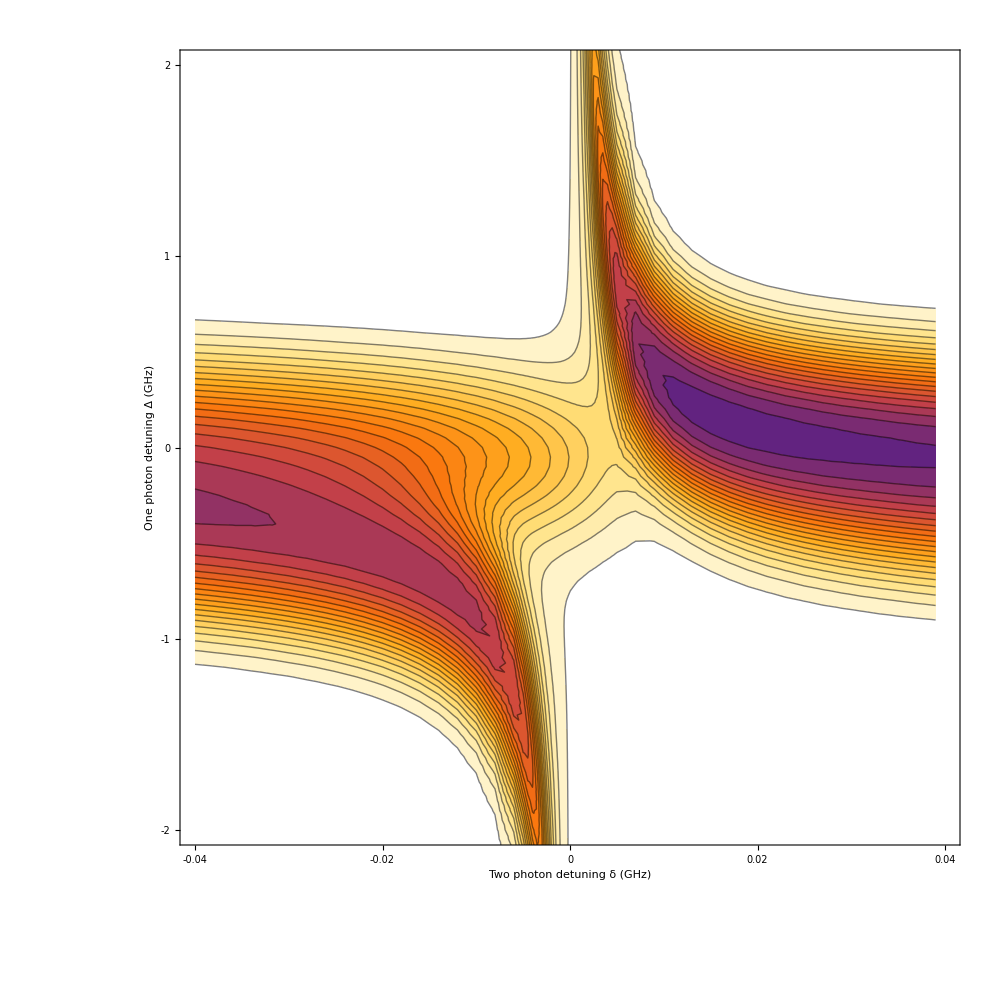

```mathematica
kkkkkk5=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev4DoppTestv[47,100/1000,1.0/1000,0.8*10^6,delt*10^9,1,0]}],{delt,
Flatten[{Range[-0.040,-0.005,0.002],Range[-0.005,0.005,0.0005],Range[0.005,0.04,0.002]}]}]],3];
Kiakkk5=ListContourPlot[kkkkkk5,Contours->25,FrameTicks->{{{-3,-2,-1,0,1,2,3},None},{{-0.04,-0.02,0,0.02,0.04},None}},FrameTicksStyle->Directive[40]
,ImageSize->1000,ColorFunction->(ColorData["SunsetColors"][Rescale[#,{0,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic,PlotRange->{{-0.04,0.04},{-2,2},{0,1}},FrameLabel->{Style["Two photon detuning δ (GHz)",50,Black],Style["One photon detuning Δ (GHz)",50,Black]}]
```

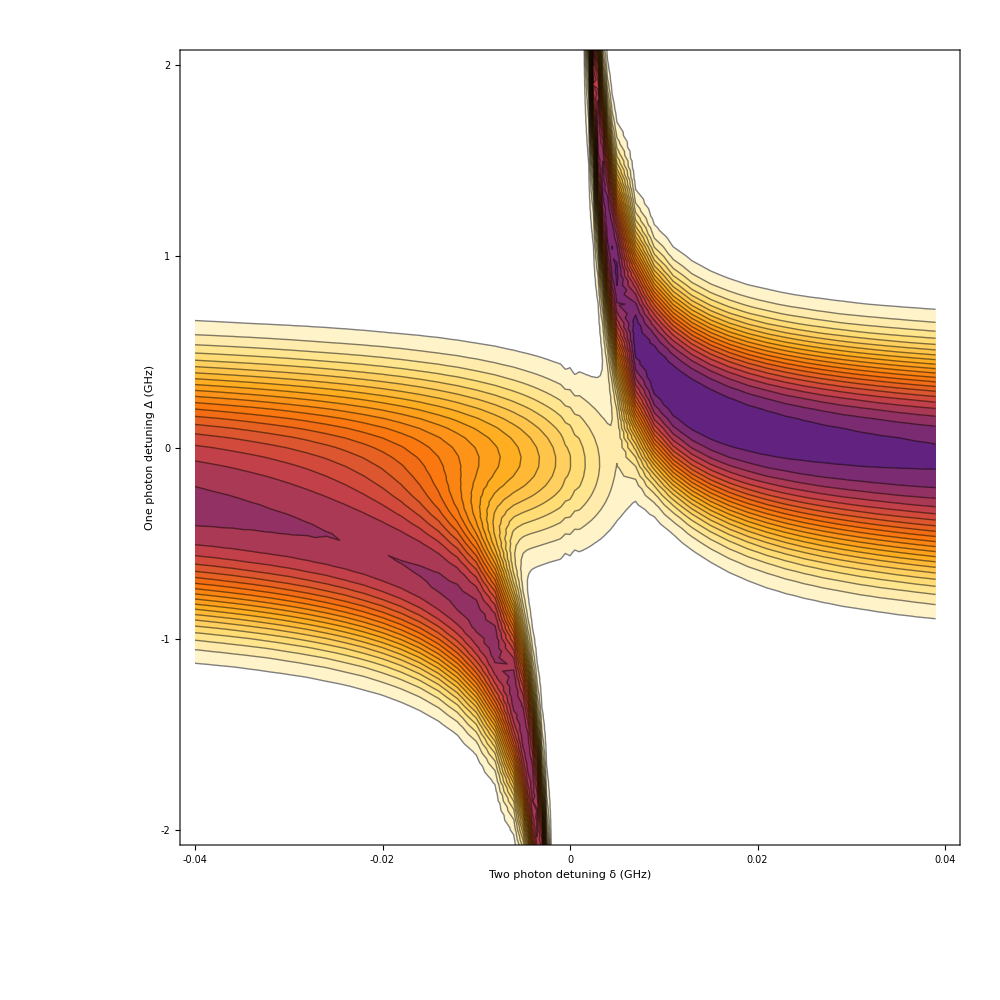

```mathematica
kkkkkk5=Partition[Flatten[Table[Transpose[{Table[delt,{i,1,201}],Lev4DoppTestv[47,100/1000,1.0/1000,0.1*10^6,delt*10^9,1,0]}],{delt,
Flatten[{Range[-0.040,-0.005,0.002],Range[-0.005,0.005,0.0005],Range[0.005,0.04,0.002]}]}]],3];
Kiakkk5=ListContourPlot[kkkkkk5,Contours->25,FrameTicks->{{{-3,-2,-1,0,1,2,3},None},{{-0.04,-0.02,0,0.02,0.04},None}},FrameTicksStyle->Directive[40]
,ImageSize->1000,ColorFunction->(ColorData["SunsetColors"][Rescale[#,{0,1}]]&),ColorFunctionScaling->False,ClippingStyle->Automatic,PlotRange->{{-0.04,0.04},{-2,2},{0,1}},FrameLabel->{Style["Two photon detuning δ (GHz)",50,Black],Style["One photon detuning Δ (GHz)",50,Black]}]
```

## d

```mathematica
Reson1=Select[data35,-0.003<#[[2]]<0.003&][[All,{1,3}]];
```

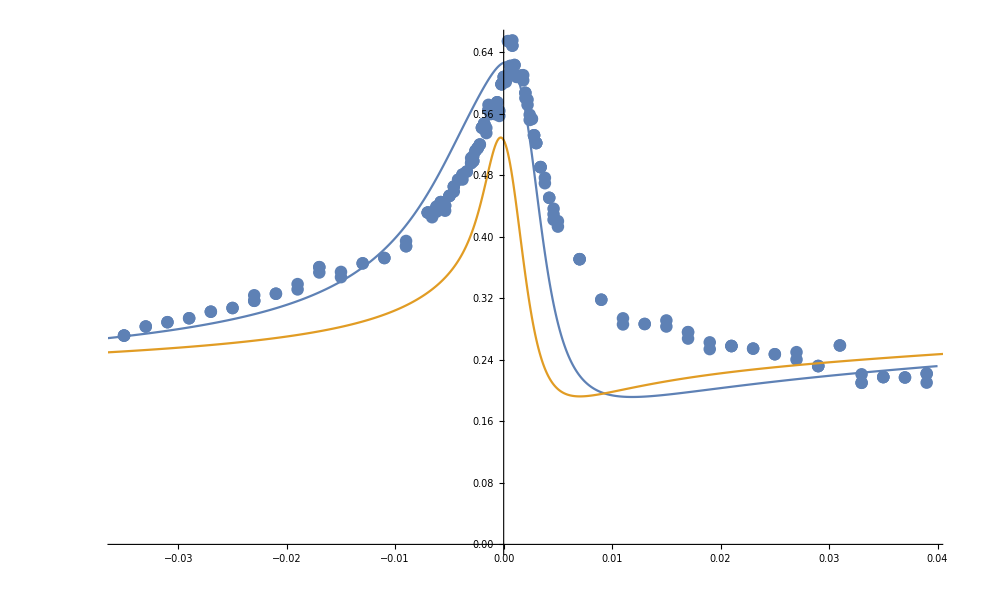

```mathematica
Show[ListPlot[Reson1],ListPlot[{Lev4DoppTestsc[47,35/1000,1.0/1000,1.4*10^6,0*10^9],Lev3DoppTestsc[47,35/1000,1.0/1000,1.4*10^6,0*10^9]},Joined->True]]
```

Select::normal: Nonatomic expression expected at position 1 in Select[data100,δ-0.003<#1⟦2⟧<δ+0.003&].

Part::partd: Part specification Select[data100,δ-0.003<#1⟦2⟧<δ+0.003&]⟦All,{1,3}⟧ is longer than depth of object.

Select::normal: Nonatomic expression expected at position 1 in Select[data100,δ-0.003<#1⟦2⟧<δ+0.003&].

Part::partd: Part specification Select[data100,δ-0.003<#1⟦2⟧<δ+0.003&]⟦All,{1,3}⟧ is longer than depth of object.

ListPlot::lpn: Select[data100,δ-0.003<#1⟦2⟧<δ+0.003&]⟦All,{1,3}⟧ is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListPlot[Select[data100,δ-0.003<Slot[«1»]⟦2⟧<δ+0.003&]⟦All,{1,3}⟧],].

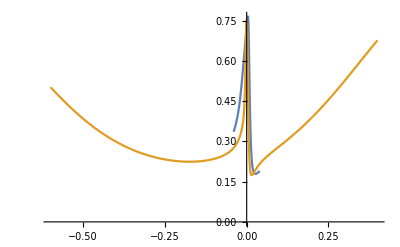
Show[ListPlot[Select[data100,δ-0.003<#1⟦2⟧<δ+0.003&]⟦All,{1,3}⟧],-Graphics-]

```mathematica
δ=0;
Reson=Select[data100,δ-0.003<#[[2]]<δ+0.003&][[All,{1,3}]];
Show[ListPlot[Reson],ListPlot[{Lev4DoppTestsc[47,100/1000,1.0/1000,1.4*10^6,δ*10^9],Lev3DoppTestsc[47,100/1000,1.0/1000,1.4*10^6,δ*10^9]},Joined->True]]
```

```mathematica
δ=0;
Reson0=Select[data,δ-0.003<#[[2]]<δ+0.003&][[All,{1,3}]];
Show[ListPlot[Reson0],ListPlot[{Lev4DoppTestsc[47,1/1000,1.0/1000,1.4*10^6,δ*10^9],Lev3DoppTestsc[47,1/1000,1.0/1000,1.4*10^6,δ*10^9]},Joined->True]]
```

-Graphics-

```mathematica
δ=0;
γ=1.4;
Reson0=Select[data,δ-0.003<#[[2]]<δ+0.003&][[All,{1,3}]];
Show[ListPlot[Reson0,PlotRange->{0,1},Frame->True,Axes->False],ListPlot[{Lev4DoppTestsc[47,1/1000,1.0/1000,γ*10^6,δ*10^9],Lev3DoppTestsc[47,1/1000,1.0/1000,γ*10^6,δ*10^9]},Joined->True]]
```

-Graphics-